```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4330,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{}

```mathematica
quarkAData = Table[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[yu];myd=Minors[yd];
QuarkAMatrices[yu, yd, myu, myd]
,{i,Length[quarkData]}
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[quarkAData]
```

{0.92443,Null}

{1321,4,3,3}

```mathematica
leptonADataNH = Table[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,1]
,{i,Length[leptonData[[1]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataNH]
```

{1.57149,Null}

{4330,2,3,3}

#### Values

```mathematica
Amean = Mean[Abs[quarkAData]];
MatrixForm/@Amean
```

{(1 | 0.146935 | 0.00814545
0.146935 | 1 | 0.0345075
0.00487235 | 0.0345075 | 1),(1. | 0.0175847 | 0.000856618
0.0175847 | 1. | 0.0576862
0.00105984 | 0.0576862 | 1.),(1 | 0.148202 | 0.00427156
0.148202 | 1 | 0.0279882
0.00790462 | 0.0279882 | 1),(1. | 0.14366 | 0.0855266
0.14366 | 1. | 0.198603
0.0803869 | 0.198603 | 1.)}

```mathematica
AmeanLog = Log10[Mean[Abs[quarkAData]]];
MatrixForm/@AmeanLog
```

{(0 | -0.832875 | -2.08909
-0.832875 | 0 | -1.46209
-2.31226 | -1.46209 | 0),(0. | -1.75486 | -3.06721
-1.75486 | 0. | -1.23893
-2.97476 | -1.23893 | 0.),(0 | -0.829147 | -2.36941
-0.829147 | 0 | -1.55302
-2.10212 | -1.55302 | 0),(0. | -0.842664 | -1.0679
-0.842664 | 0. | -0.702014
-1.09481 | -0.702014 | 0.)}

```mathematica
Asdev = StandardDeviation[Log10[Abs[quarkAData]]];
MatrixForm/@Asdev
```

{(0. | 0.352654 | 0.515803
0.352654 | 0. | 0.384498
0.384812 | 0.384498 | 0.),(5.11062×10^-18 | 0.506977 | 0.611748
0.506977 | 4.38317×10^-18 | 0.542753
0.496973 | 0.542753 | 3.96775×10^-18),(0. | 0.344755 | 0.493118
0.344755 | 0. | 0.434169
0.466812 | 0.434169 | 0.),(3.50189×10^-18 | 0.389586 | 0.444044
0.389586 | 4.76137×10^-18 | 0.428242
0.421583 | 0.428242 | 4.76137×10^-18)}

```mathematica
Amean = Mean[Abs[leptonADataNH]];
MatrixForm/@Amean
```

{(1 | 0.177143 | 0.067641
0.177143 | 1 | 0.188211
0.0634634 | 0.188211 | 1),(1. | 0.03282 | 0.00451576
0.03282 | 1. | 0.11704
0.00429479 | 0.11704 | 1.)}

```mathematica
AmeanLog = Log10[Mean[Abs[leptonADataNH]]];
MatrixForm/@AmeanLog
```

{(0 | -0.751675 | -1.16979
-0.751675 | 0 | -0.725355
-1.19748 | -0.725355 | 0),(0. | -1.48386 | -2.34527
-1.48386 | 0. | -0.931668
-2.36706 | -0.931668 | 0.)}

```mathematica
Asdev = StandardDeviation[Log10[Abs[leptonADataNH]]];
MatrixForm/@Asdev
```

{(0. | 0.395444 | 0.494362
0.395444 | 0. | 0.414123
0.445046 | 0.414123 | 0.),(4.61334×10^-18 | 0.578405 | 0.644163
0.578405 | 5.10067×10^-18 | 0.50886
0.552289 | 0.50886 | 4.49758×10^-18)}

#### Graphs

```mathematica
getADataAbs[data_,entry_]:=Grid[Table[Histogram[Table[data[[mat,entry]][[i,j]],{mat,1,Length[data]}]//Abs//Log10//Threshold,{"Raw",15}],
{i,1,3},{j,1,3}]]
```

```mathematica
getADataArg[data_,entry_]:=Grid[Table[Histogram[Table[data[[mat,entry]][[i,j]],{mat,1,Length[data]}]//Arg,{"Raw",15}],
{i,1,3},{j,1,3}]]
```

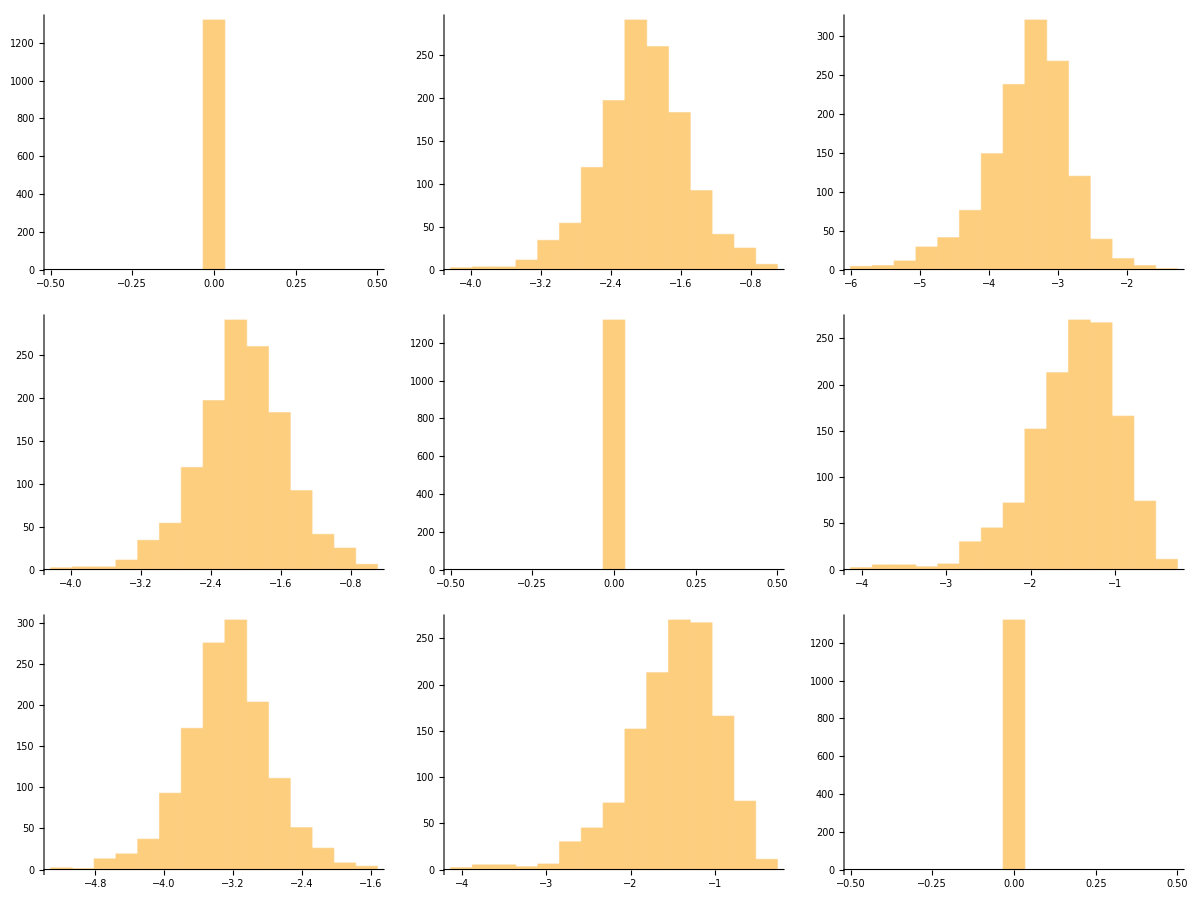

```mathematica
auR=getADataAbs[quarkAData,2]
```

```mathematica
(*  Export["Output/hist_AuR.jpg",auR] *)
```

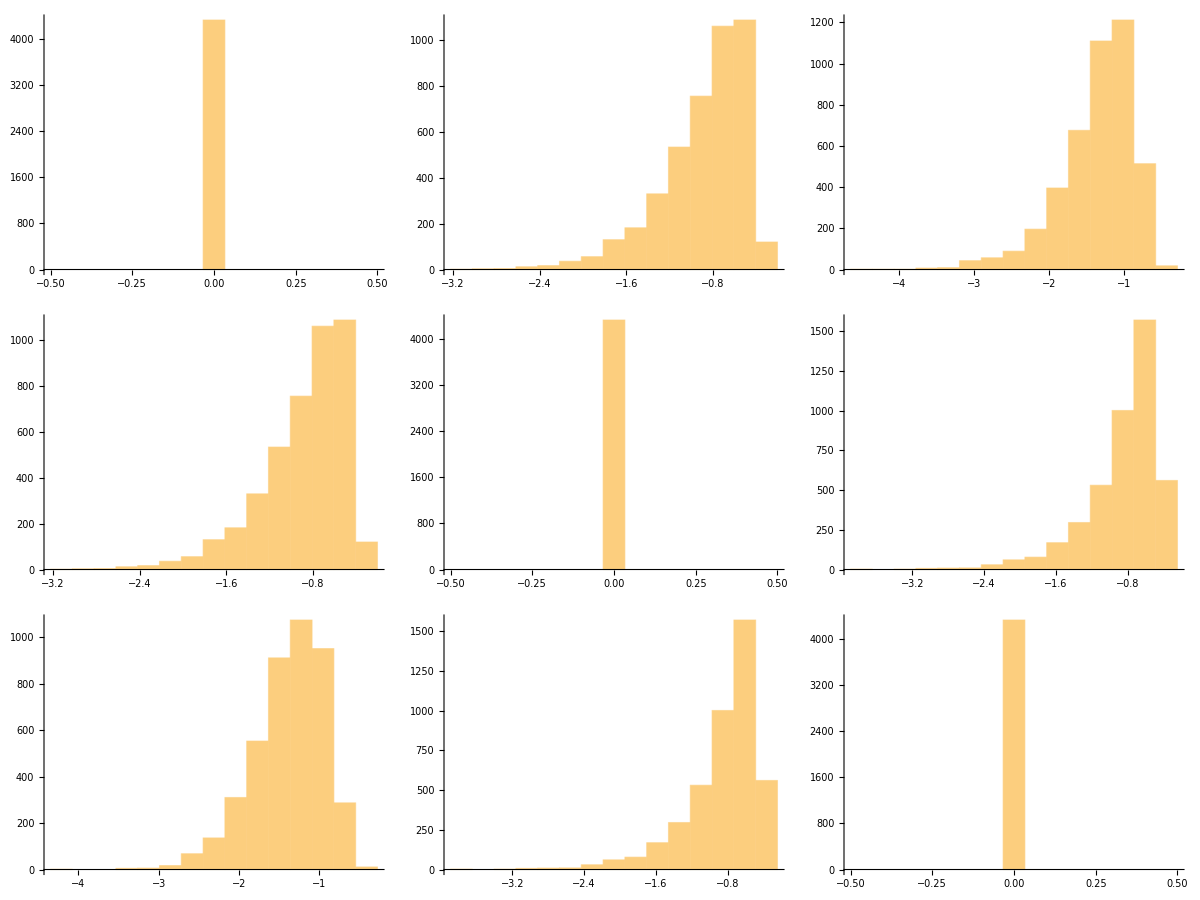

```mathematica
ael=getADataAbs[leptonADataNH,1]
```

```mathematica
(* Export["Output/hist_AeL.jpg",ael] *)
```

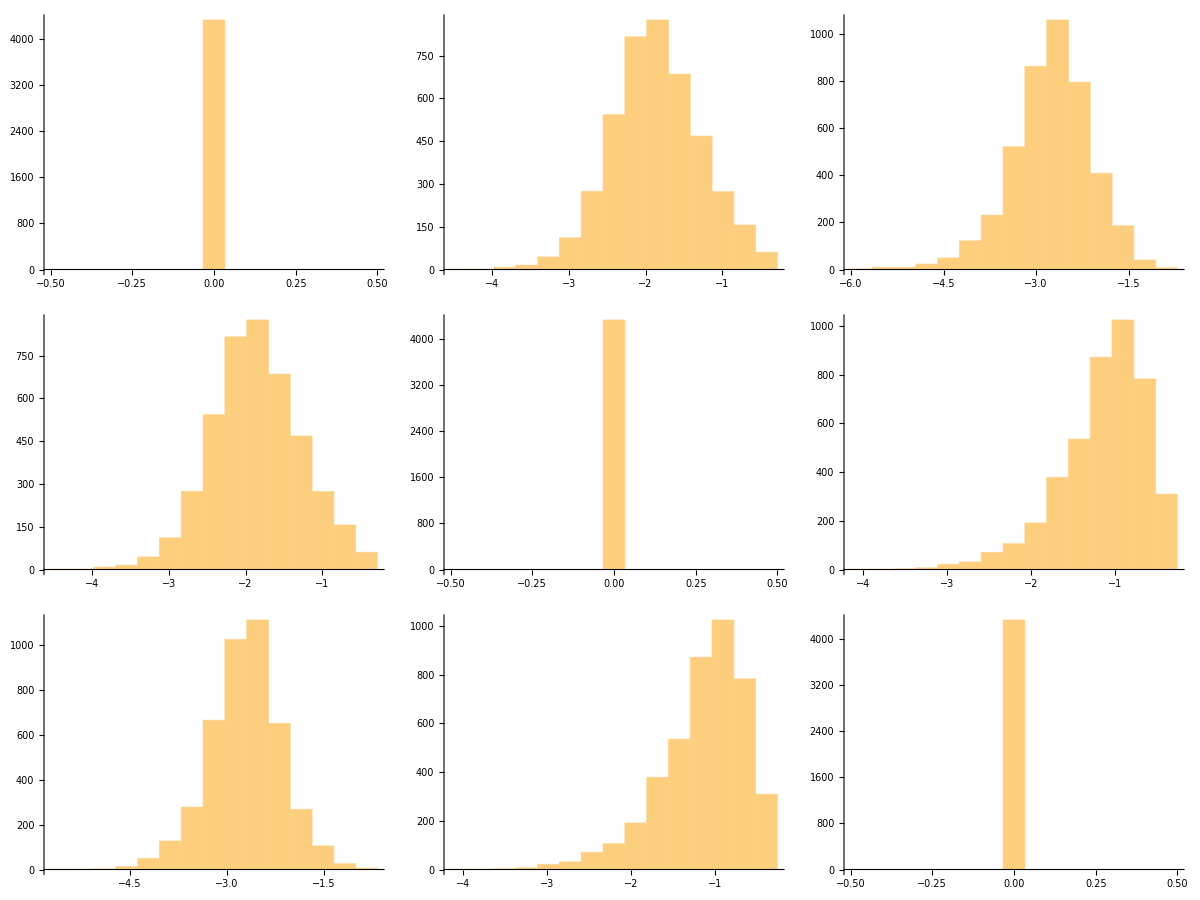

```mathematica
aeR = getADataAbs[leptonADataNH,2]
```

```mathematica
(* Export["Output/hist_AeR.jpg",aeR] *)
```

```mathematica
newHistogram[data_]:=Module[{pdfs},
pdfs=PDF[EstimatedDistribution[data,NormalDistribution[mu,sigma]],x];Show[{Histogram[data,15,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-4,-1},Automatic}],Plot[pdfs,{x,Min[data],Max[data]}]}]
]
```

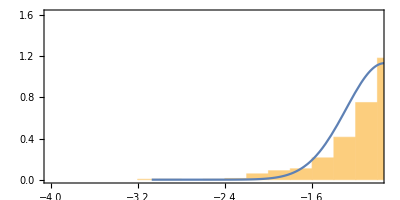

```mathematica
newHistogram @(Table[quarkAData[[mat,1]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )
```

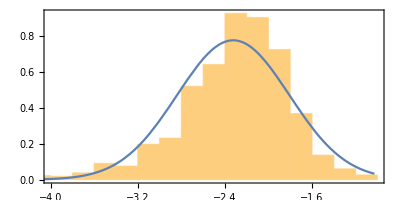

```mathematica
newHistogram @(Table[quarkAData[[mat,1]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )
```

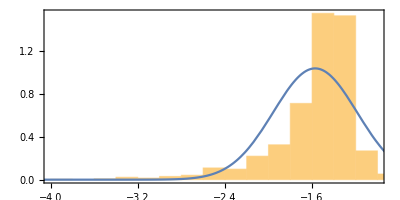

```mathematica
newHistogram @(Table[quarkAData[[mat,1]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )
```

```mathematica
cubeHelixColor[l_,s_,r_,h_,g_]:=With[
{ψ=2 π (s/3+r l),a=h l^g (1-l^g)/2},
RGBColor[
l^g+a{{-0.14861,1.78277},{-0.29227,-0.90649},{1.97294,0.0}}.{Cos[ψ],Sin[ψ]}
]
]
```

```mathematica
colorsStandard = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
colors=Table[
cubeHelixColor[0.5,s,π/6,1,1],
{s,{0,0.15,0.3,0.5,0.8,1,1.5,1.8,2.0,2.2,2.4,2.6}}
]//Flatten
```

{RGBColor[{0.7236100438261407, 0.3897060587723205, 0.48173308035896434}],RGBColor[{0.7132897054833467, 0.40895632946827126, 0.40662747026197715}],RGBColor[{0.6820910846910813, 0.43711858897442013, 0.3406618139404164}],RGBColor[{0.6135535576997629, 0.4836737789354366, 0.2778762042137195}],RGBColor[{0.4786343604757513, 0.5561096332061026, 0.25731664278722743}],RGBColor[{0.38994351387362236, 0.593967720163116, 0.2961431238547551}],RGBColor[{0.27638995617385936, 0.6102939412276795, 0.5182669196410356}],RGBColor[{0.3179089153089188, 0.5628814110255798, 0.6593381860595837}],RGBColor[{0.38644644230023706, 0.5163262210645634, 0.7221237957862805}],RGBColor[{0.47461841101953034, 0.46694807916242187, 0.7465021832901948}],RGBColor[{0.5671790870580439, 0.42328491464037193, 0.7282581039012023}],RGBColor[{0.6481238886413754, 0.3928864853116728, 0.6705461246879174}]}

```mathematica
PlotPDF[data_,color_]:=Plot[PDF[EstimatedDistribution[data,NormalDistribution[mu,sigma]],x],{x,Min[data],Max[data]+1},PlotStyle->{Thin,color}]
```

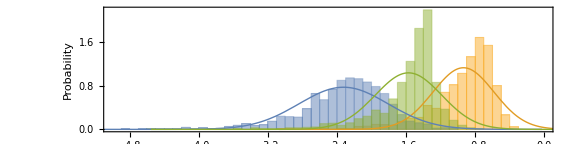

```mathematica
Show[
Histogram[{
(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )}
,13*3,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-5,0},{0,2.2}}],
PlotPDF[(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[2]]],
PlotPDF[(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[1]]],
PlotPDF[(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[3]]]
,ImageSize->Large,AspectRatio->1/4,FrameLabel->{"","Probability"}]& @ 1
```

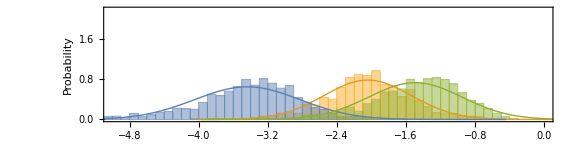

```mathematica
Show[
Histogram[{
(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )}
,13*3,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-5,0},{0,2.2}}],
PlotPDF[(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[2]]],
PlotPDF[(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[1]]],
PlotPDF[(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[3]]]
,ImageSize->Large,AspectRatio->1/4,FrameLabel->{"log_10 A_ij","Probability"}]& @ 2
```

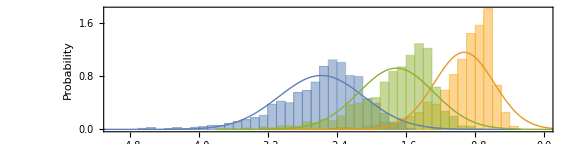

```mathematica
Show[
Histogram[{
(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )}
,13*3,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-5,0},{0,1.8}}],
PlotPDF[(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[2]]],
PlotPDF[(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[1]]],
PlotPDF[(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[3]]]
,ImageSize->Large,AspectRatio->1/4,FrameLabel->{"","Probability"}]& @ 3
```

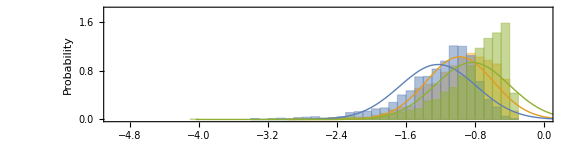

```mathematica
Show[
Histogram[{
(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),
(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold )}
,13*3,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-5,0},{0,1.8}}],
PlotPDF[(Table[quarkAData[[mat,#]][[1,2]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[2]]],
PlotPDF[(Table[quarkAData[[mat,#]][[1,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[1]]],
PlotPDF[(Table[quarkAData[[mat,#]][[2,3]],{mat,1,Length[quarkAData]}]//Abs//Log10//Threshold ),colorsStandard[[3]]]
,ImageSize->Large,AspectRatio->1/4,FrameLabel->{"log_10 A_ij","Probability"}]& @ 4
```

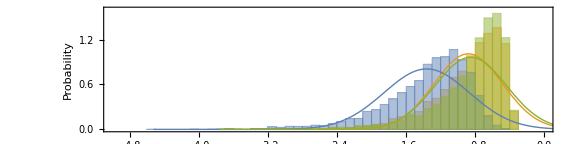

```mathematica
Show[
Histogram[{
(Table[leptonADataNH[[mat,#]][[1,2]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),
(Table[leptonADataNH[[mat,#]][[1,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),
(Table[leptonADataNH[[mat,#]][[2,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold )}
,13*3,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-5,0},{0,1.6}}],
PlotPDF[(Table[leptonADataNH[[mat,#]][[1,2]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),colorsStandard[[2]]],
PlotPDF[(Table[leptonADataNH[[mat,#]][[1,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),colorsStandard[[1]]],
PlotPDF[(Table[leptonADataNH[[mat,#]][[2,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),colorsStandard[[3]]]
,ImageSize->Large,AspectRatio->1/4,FrameLabel->{"","Probability"}]& @ 1
```

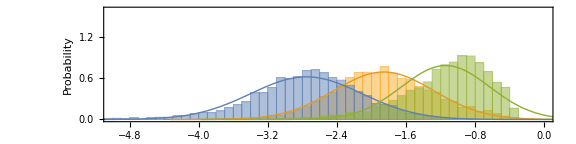

```mathematica
Show[
Histogram[{
(Table[leptonADataNH[[mat,#]][[1,2]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),
(Table[leptonADataNH[[mat,#]][[1,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),
(Table[leptonADataNH[[mat,#]][[2,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold )}
,13*3,"ProbabilityDensity",AspectRatio->1/2,Frame->True,PlotRange->{{-5,0},{0,1.6}}],
PlotPDF[(Table[leptonADataNH[[mat,#]][[1,2]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),colorsStandard[[2]]],
PlotPDF[(Table[leptonADataNH[[mat,#]][[1,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),colorsStandard[[1]]],
PlotPDF[(Table[leptonADataNH[[mat,#]][[2,3]],{mat,1,Length[leptonADataNH]}]//Abs//Log10//Threshold ),colorsStandard[[3]]]
,ImageSize->Large,AspectRatio->1/4,FrameLabel->{"log_10 A_ij","Probability"}]& @ 2
```